```mathematica
Clear["Global`*"];
Off[NIntegrate::slwcon];Off[NIntegrate::ncvb];Off[NIntegrate::izero];Off[NIntegrate::oidiv];Off[NIntegrate::errprec];
```

```mathematica
BasisFunction[n_]:=Function[{x},LegendreP[n,x]];
BasisMin=1;
BasisMax=15;
Plot[Evaluate[Table[BasisFunction[n][x],{n,BasisMin,BasisMax}]],{x,-1,1},ImageSize->Medium,PlotRange->All];
```

```mathematica
PolinomeToCartesianBasis[y_]:=y.Table[BasisFunction[n][x],{n,BasisMin,BasisMax}];
```

```mathematica
qFunction[x_]=PDF[NormalDistribution[0.1,0.2],x];
q=Table[NIntegrate[qFunction[x]BasisFunction[n][x],{x,-1,1}],{n,BasisMin,BasisMax}];
Plot[{qFunction[x],PolinomeToCartesianBasis[q]},{x,-1,1},PlotRange->All];
```

```mathematica
L=Table[NIntegrate[(D[BasisFunction[m][x], x])×(D[BasisFunction[n][x], x]),{x,-1,1}],{n,BasisMin,BasisMax},{m,BasisMin,BasisMax}];
```

```mathematica
a=2;b=-1;
aRow=Table[a (BasisFunction[n][x])/.{x->-1},{n,BasisMin,BasisMax}];
bRow=Table[b (BasisFunction[n][x])/.{x->+1},{n,BasisMin,BasisMax}];
```

```mathematica
CoordinatesTable=Table[Subscript[c, i],{i,BasisMin,BasisMax}];
Functional=Chop[L.CoordinatesTable.CoordinatesTable-2q.CoordinatesTable-2(bRow.CoordinatesTable-aRow.CoordinatesTable)];
```

```mathematica
Coordinates=CoordinatesTable/.NMinimize[Functional,CoordinatesTable][[2]];
```

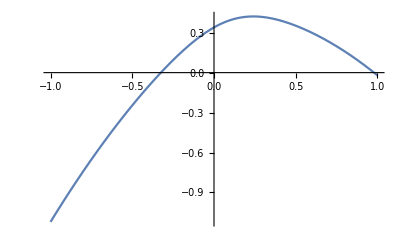

```mathematica
Plot[PolinomeToCartesianBasis[Coordinates],{x,-1,1}]
```

```mathematica
{D[PolinomeToCartesianBasis[Coordinates],x]/.{x->-1},D[PolinomeToCartesianBasis[Coordinates],x]/.{x->+1}}
```

{1.99943,0.998487}

```mathematica
Total[D[Functional,{CoordinatesTable}]]/.{Table[Subscript[c, i]->Coordinates[[i]],{i,BasisMin,BasisMax}]};
```

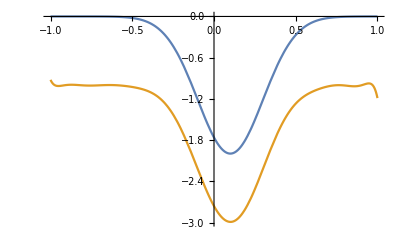

```mathematica
Plot[Evaluate[{-qFunction[x],D[PolinomeToCartesianBasis[Coordinates], x,x]}],{x,-1,1}]
```

I = ∫(u_x^2- 2 q u)dx - 2 (b u|_1-au|_-1)
δ I = ∫(2 u_x h_x +h_x^2- 2 q h)  dx 2 (b h|_1-ah|_-1) = ∫h_x^2dx-∫(u_(x,x)-  q) h dx + 2 h (u_x-b)|_1 - 2 h (u_x-a)|_-1